```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
networks100Fixed=Table[Import[StringJoin["graphs/model-v3/fixed/","network-100-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

```mathematica
red=networks100Fixed[[1]]
```

-Graphics-

```mathematica
GlobalClusteringCoefficient[red]
```

9/56

```mathematica
Mean[VertexDegree[red]]
```

9/5

```mathematica
PDF[PoissonDistribution[λ],k]
```

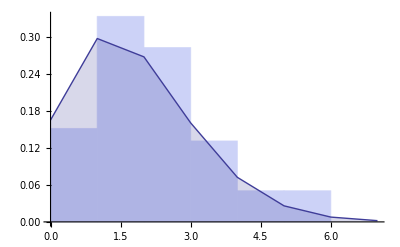

```mathematica
Show[
Histogram[VertexDegree[red],{Min[VertexDegree[red]],Max[VertexDegree[red]],1},"PDF"],
DiscretePlot[PDF[PoissonDistribution[9/5],x],{x,Min[VertexDegree[red]],Max[VertexDegree[red]]},PlotStyle->PointSize[Medium],Joined->True]]
```

```mathematica
Distr[red_]:=Module[{},
Show[
Histogram[VertexDegree[red],{Min[VertexDegree[red]],Max[VertexDegree[red]],1},"PDF"],
DiscretePlot[PDF[PoissonDistribution[Mean[VertexDegree[red]]],x],{x,Min[VertexDegree[red]],Max[VertexDegree[red]]},PlotStyle->PointSize[Medium],Joined->True]]
];
```

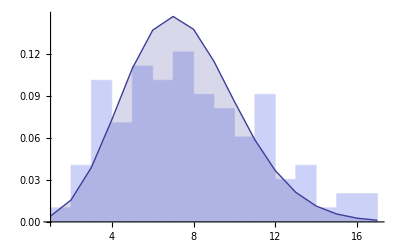
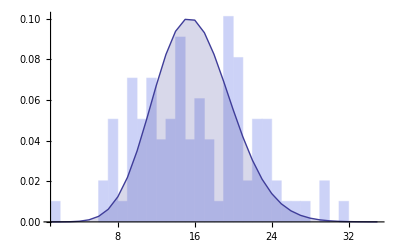
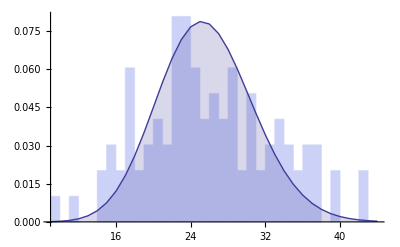
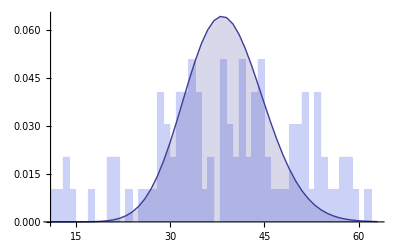
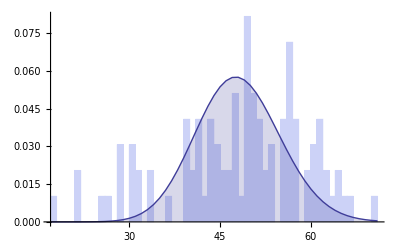
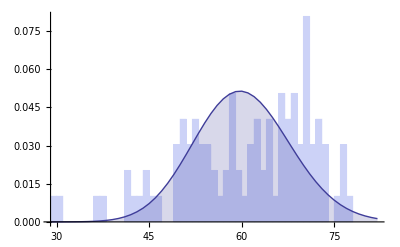
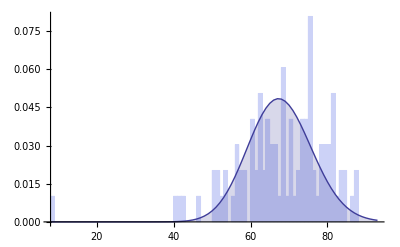
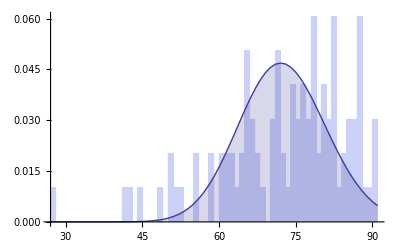
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Distr[networks100Fixed[[i]]],{i,1,10,1}]
```

```mathematica
PDF[PoissonDistribution[Mean[VertexDegree[red]]],x]
```

Piecewise[{{(9/5)^x/(ⅇ^(9/5) x!), x≥0}, {0, True}}]

```mathematica
line = LinearModelFit[VertexDegree[red], {PDF[PoissonDistribution[Mean[VertexDegree[red]]],x],x},x]
```

FittedModel[1.84905-0.00108149 x+0.666256 (Piecewise[{{(9/5)^x/(ⅇ^(9/5) x!), x≥0}, {0, True}}])]

```mathematica
line[{"RSquared","ANOVATable"}]
```

{0.00123831, | DF | SS | MS | F-Statistic | P-Value
Piecewise[{{(9/5)^x/(ⅇ^(9/5) x!), x≥0}, {0, True}}] | 1 | 0.150589 | 0.150589 | 0.076173 | 0.783139
x | 1 | 0.0871667 | 0.0871667 | 0.0440919 | 0.834123
Error | 97 | 191.762 | 1.97693 |  | 
Total | 99 | 192. |  |  | }